```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"];
<<MaTeX`;
MaTeX["x^2"] (*Este bloque echa a andar MaTeX. Para tener tipografia tipo LaTeX*)
```

Import::nfurl: Unable to retrieve data from https://api.github.com/repos/szhorvat/MaTeX/releases/latest. Consult Internal`$LastInternalFailure for potential information.

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
BoltzmannConstant=1.380649*10^-23;(*J/K*)
PlanckConstant = 6.626068*10^-34/2π;(*Js*)
densidad  = 5.317*1/1000*100/1*100/1*100/1;(*Kg*m^-3*)
YoungModule=8.59*10^-5/1*100/1*100/1*100/1;(*N*m^-3*)
ν=1/3;
velocidad=4*10^5*1/100;
altura=200*10^-9;
ancho = 300*10^-9;
largo = 10*10^-6;
rigidez=YoungModule*altura^3/(12*(1-ν^3));
ωRing=(√(rigidez/(densidad*altura)))/ancho^2;
a = 0.01;
aPrime = 0.01;
```

```mathematica
coeficienteB[ω_, k_]:=-(ω+(1-ν)k^2 Cosh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Cos[(√(ω+k^2))/2])*a;
coeficienteBPrima[ω_, k_]:=-(ω+(1-ν)k^2 Sinh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Sin[(√(ω+k^2))/2])*aPrime;
```

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]+
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->20]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= waveNumber^2+offset;
```

```mathematica
amplitudWSim[k_,y_,off_]:=Re[(a*Cosh[√(frecuenciaωSimPositivo[k, off]+k^2)*y]+coeficienteB[frecuenciaωSimPositivo[k, off],k]*Cos[√(frecuenciaωSimPositivo[k, off]-k^2)*y])/√(1/2 (a^2+b^2+b^2 Cos[2 √(k^2+ω)]+(a (8 b Cos[√(k^2+ω)] Sinh[(√(k^2+ω))/2]+a Sinh[√(k^2+ω)]))/(√(k^2+ω)))/.{b->coeficienteB[frecuenciaωSimPositivo[k, off],k], ω->frecuenciaωSimPositivo[k, off]})];
amplitudWAntiSim[k_,y_,off_]:=aPrime*Sinh[√(frecuenciaωAntiSimPositivo[k, off]+k^2)*y]/√(1/2 aPrime^2 (-1+Sinh[√(k^2+ω)]/(√(k^2+ω)))/.{ω->frecuenciaωAntiSimPositivo[k, off]});
```

```mathematica
distribucionBE[frecuencia_,temp_] := 1/(Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)]-1);
distribucionMB[frecuencia_, temp_]:=1/Exp[(PlanckConstant*frecuencia)/(BoltzmannConstant*temp)];
BE[x_] := 1/(Exp[x]-1);
MB[x_]:=1/Exp[x];
```

6.26394×10^-6 frecuenciaωSimPositivo[(9 π)/5,0]

```mathematica
PlanckConstant*frecuenciaωSimPositivo[2*π*30*ancho/largo, 0]*ωRing
```

2.71294×10^-27

```mathematica
BoltzmannConstant*1
```

1.38065×10^-23

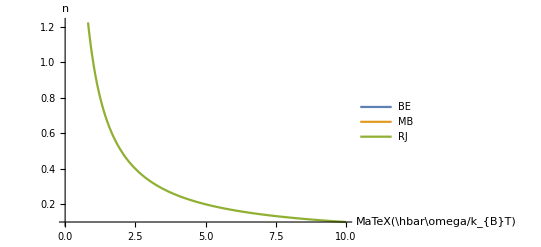

```mathematica
comparaDistros = Plot[{BE[x],MB[x],1/x},{x, 0,10}, PlotLegends->{BE, MB, RJ}, AxesLabel->{MaTeX["\\hbar\\omega/k_{B}T"],"n"}]
```

```mathematica
Export["compareDistributions.pdf", comparaDistros]
```

compareDistributions.pdf

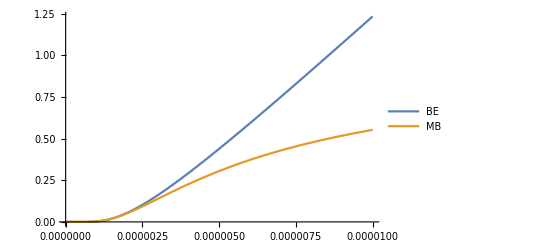

```mathematica
Plot[{distribucionBE[frecuenciaωSimPositivo[1, 0]*ωRing,t], distribucionMB[frecuenciaωSimPositivo[1,0]*ωRing, t]}, {t, 0,0.00001}, PlotLegends->{BE,MB}]
```

```mathematica
temperatura=PlanckConstant*velocidad/(BoltzmannConstant*ancho)
```

1.00515

```mathematica
meanSquaredDisplacement[y_]:=PlanckConstant/(densidad*largo*ancho*altura)*Sum[(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementRJ[y_]:=(BoltzmannConstant*(temperatura1+temperatura2))/(densidad*largo*ancho*altura)*Sum[(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]ωRing)^2),{n,1, 30}];
meanSquaredDisplacementAntiRJ[y_]:=(BoltzmannConstant*(temperatura1+temperatura2))/(densidad*largo*ancho*altura)*Sum[(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]ωRing)^2),{n,1, 30}];
meanSquaredDisplacementMB[y_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]ωRing))*(distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementAnti[y_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquaredDisplacementAntiMB[y_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}]
meanSquaredDisplacementAntiBE[y_]:=Sum[PlanckConstant/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}]
```

```mathematica
meanSquaredDisplacement[0.]
meanSquaredDisplacementRJ[0.5]
meanSquaredDisplacementAntiMB[0.5]
meanSquaredDisplacementAntiMB[0.0]
```

4.78767×10^-15

4.35076×10^-15

2.22509×10^-21

0.

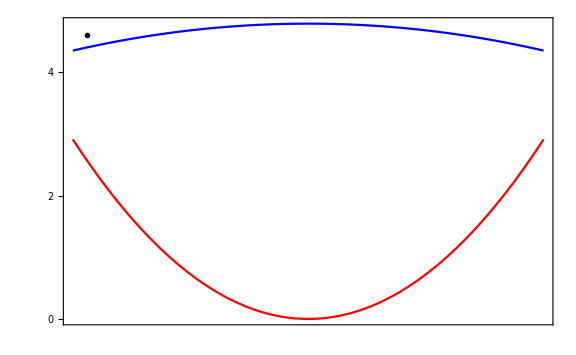

```mathematica
msdSimBE=Plot[{ meanSquaredDisplacementRJ[y], meanSquaredDisplacementAntiRJ[y]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-15} \\mathrm{m}^{2})", Magnification->2], None},{
None, None}
},
FrameTicks->{
{Table[{j*10^-15,Style[ToString[j], Black]},{j,Range[0,5,2]}], False(* y axis*)},{Table[{j, ""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(a)}", Magnification->2],{-0.47,4.6*10^-15}]]
```

```mathematica
Export["msdBE.pdf",msdSimBE]
```

msdBE.pdf

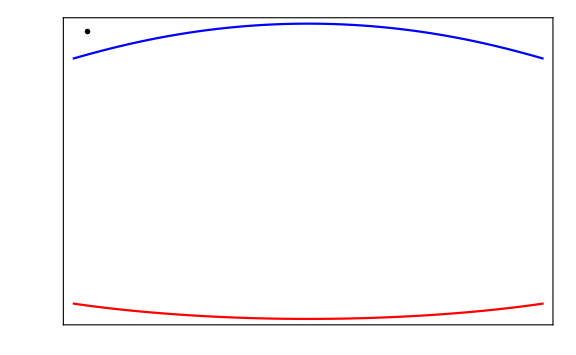

```mathematica
msdSimMB=Plot[{meanSquaredDisplacementMB[y], meanSquaredDisplacementAntiMB[y]},{y, -0.5,0.5},PlotRange->Full,  PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{None,MaTeX["\\left\\langle \\hat{\\xi}^{2} \\right\\rangle (\\times 10^{-21} \\mathrm{m}^{2})", Magnification->2]},{
None, None}
},
FrameTicks->{
{Table[{j*10^-21,""},{j,Range[0,5,2]}],Table[{j*10^-21,Style[ToString[j], Black]},{j,Range[0,5,2]}](* y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(b)}", Magnification->2],{-0.47,4.2*10^-21}]]
```

```mathematica
Export["msdMB.pdf",msdSimMB]
```

msdMB.pdf

```mathematica
meanSquaredDisplacementMB[0.5]
meanSquaredDisplacementMB[0.0]
```

3.80159×10^-21

4.31376×10^-21

```mathematica
Export["meanQuadraticSymmetric.pdf",%]
```

meanQuadraticSymmetric.pdf

```mathematica
Corriente[y_]:=(BoltzmannConstant*velocidad^2*(temperatura1-temperatura2))/(largo*altura*ancho)*Sum[(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing), {n, 1, 30}];
CorrienteAnti[y_]:=(BoltzmannConstant*velocidad^2*(temperatura1-temperatura2))/(largo*altura*ancho)*Sum[(2π*n/largo)*amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2/(frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing), {n, 1, 30}];
CorrienteMB[y_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWSim[2π*n*ancho/largo,y,0.0]^2* (distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}];
CorrienteAntiMB[y_]:=Sum[(PlanckConstant*velocidad^2)/(largo*altura*ancho)*(2π*n/largo)*amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2* (distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] -distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] ), {n, 1, 30}]
```

```mathematica
Corriente[0.0]
```

7.45716×10^6

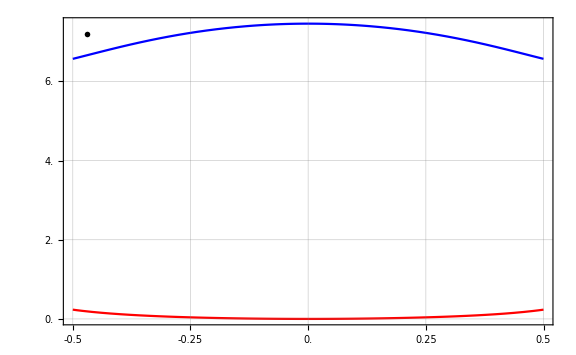

```mathematica
corrientePlotBE=Plot[{Corriente[y], CorrienteAnti[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{J} \\right\\rangle (10^{6} \\mathrm{J}/\\mathrm{m}^{2}\\mathrm{s})", Magnification->2], None},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^6,Style[ToString[j], Black]},{j,Range[0.0,10,2]}],False (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(c)}", Magnification->2],{-0.47,7.2*10^6}]]
```

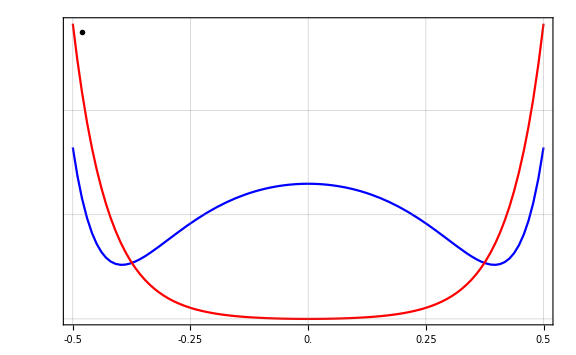

```mathematica
corrientePlotMB=Plot[{CorrienteMB[y], CorrienteAntiMB[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{None,MaTeX["\\left\\langle \\hat{J} \\right\\rangle (10^{-4} \\mathrm{J}/\\mathrm{m}^{2}\\mathrm{s})", Magnification->2]},{
MaTeX["y/W", Magnification->2], None}
},
FrameTicks->{
{Table[{j*10^-4,""},{j,Range[0.0,6,2]}],Table[{j*10^-4,Style[ToString[j], Black]},{j,Range[0.0,6,2]}] (*y axis*)},{Table[{j,j},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(f)}", Magnification->2],{-0.48,5.5*10^-4}]]
```

```mathematica
Export["corrienteMB.pdf",corrientePlotMB]
```

corrienteMB.pdf

```mathematica
meanSquareVelocitySimBE[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquareVelocitySimRJ[y_]:=((temperatura1-temperatura2)*BoltzmannConstant)/(densidad*largo*ancho*altura)*Sum[amplitudWSim[2π*n*ancho/largo,y,0.0]^2,{n,1, 30}];
meanSquareVelocityAntiSimRJ[y_]:=((temperatura1-temperatura2)*BoltzmannConstant)/(densidad*largo*ancho*altura)*Sum[amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2,{n,1, 30}];
```

```mathematica
meanSquareVelocityAntiSimBE[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionBE[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
meanSquareVelocitySimMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
```

```mathematica
meanSquareVelocityAntiSimMB[y_]:=Sum[(PlanckConstant/(2π))/(densidad*largo*ancho*altura)*(amplitudWAntiSim[2π*n*ancho/largo,y,0.0]^2*(frecuenciaωAntiSimPositivo[2π*n*ancho/largo, 0.0]*ωRing))*(distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura1] +distribucionMB[frecuenciaωAntiSimPositivo[2π*n*ancho/largo,0]*ωRing,temperatura2] +2),{n,1, 30}];
```

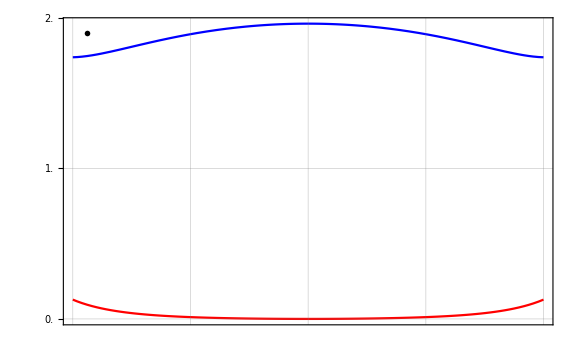

```mathematica
velocityPlotBE=Plot[{meanSquareVelocitySimRJ[y], meanSquareVelocityAntiSimRJ[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-6} \\mathrm{m}/\\mathrm{s})", Magnification->2], None},{
None, None}
},
FrameTicks->{
{Table[{j*10^-6,Style[ToString[j], Black]},{j,Range[0.0,3,1]}],False (*y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(b)}", Magnification->2],{-0.47,1.9*10^-6}]]
```

```mathematica
Export["velocidadBE.pdf",velocityPlotBE]
```

velocidadBE.pdf

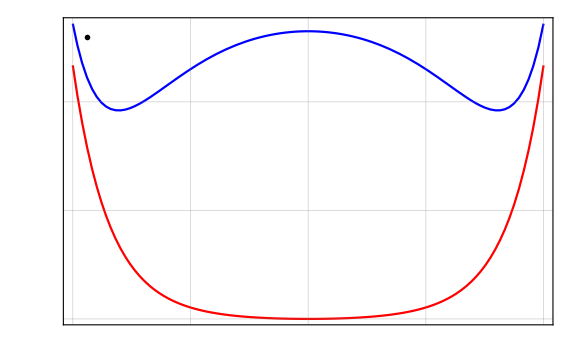

```mathematica
velocityPlotMB=Plot[{meanSquareVelocitySimMB[y], meanSquareVelocityAntiSimMB[y]},{y,-0.5,0.5}, PlotStyle->{Blue, Red}, ImageSize->Large, GridLines->Automatic,MaxRecursion->1,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, Frame->True,FrameStyle->Directive[Black, Thick],
FrameLabel->{{None,MaTeX["\\left\\langle \\hat{\\dot{\\xi}}^{2} \\right\\rangle (10^{-11} \\mathrm{m}/\\mathrm{s})", Magnification->2]},{
None, None}
},
FrameTicks->{
{Table[{j*10^-11,""},{j,Range[0.0,3,1]}] ,Table[{j*10^-11,Style[ToString[j], Black]},{j,Range[0.0,3,1]}] (*y axis*)},{Table[{j,""},{j,Range[-0.5,0.5,0.25]}](*x axis*),False}
},
Epilog->Inset[MaTeX["\\mathrm{(d)}", Magnification->2],{-0.47,2.6*10^-11}]]
```

```mathematica
Export["velocityMB.pdf",velocityPlotMB]
```

velocityMB.pdf

```mathematica
[{{msdSimBE},
{velocityPlotBE},
{corrientePlotBE}}, ImageSize->Full]
```

-Graphics-

```mathematica
Export["meanValuesRJ.pdf",%]
```

meanValuesRJ.pdf